```mathematica
<<"C:\\Users\\Nick Dupuis\\Google Drive\\School\\Physics\\Quantum\\449 Quantum II\\448defs.m"
```

# 449 HW06-Nick Dupuis 6 Problems due April 20th, 18 Points

## ✓1) Townsend 13.4

### a)

We have ψ``+(2mE)/ℏ^2 ψ = (2mV)/ℏ^2 ψ thus using greens function we see: ψ = Ae^ikz+∫dx^`G(x,x^`)((2mV)/ℏ^2)ψ(x) = X + Y where X is the homogenous Solution and Y is the Particular

### b)

From G^(``)+k^2 G=δ(x-x^`) we have two cases: Piecewise[{{G_>=Ae^(ik(x-x^`)), x>x^`}, {G_<=Ae^(ik(x^`-x)), x<x^`}}] From here we integrate from x^`-ϵ  to x^`+ϵ which gives us (G_>)^`(x+ϵ)-(G_<)^`(x-ϵ) = 1 ⇒ ihA - (-ihA) = 1 ⟹A = 1/(2ihA).
Therefore we have: G = Piecewise[{{Ae^(ik(x-x^`)), x>x^`}, {Ae^(ik(x^`-x)), x<x^`}}]

### c)

We know that ψ = e^ikx so we then have that for very large negative x: ψ = e^ikx+∫e^(ik(x-x`))/(2ik)e^(ikx`)((2mV)/ℏ^2)dx` = e^ikx+re^-ikx
R = |r|^2=(|m/(ℏ^2 k)∫e^(2ikx`)V(x)dx`|)^2

### d)

T = 1-V_0/(4 E^2)sin^2(√((2m)/ℏ^2 Ea^2))=1-R. Thus using the born approximation again: R= m^2/(ℏ^4 k^2)(V_0^2/k^2)sin^2(ha) = V_0^2/(4 E^2)sin^2 a √((2mE)/ℏ^2)

## ✓2) Townsend 13.7

f=-μ/(2π ℏ^2)∫V_0 ⅇ^(-r/a)ⅇ^(ⅈ q·r)d^3 r

```mathematica
Integrate[2π ⅇ^(ⅈ q r  Cos[θ])Sin[θ],{θ,0,π}]
```

(4 π Sin[q r])/(q r)

```mathematica
Integrate[(-μ Subscript[V, 0])/(2 π ℏ^2)ⅇ^(-r/a)% r^2,{r,0,∞},Assumptions:>{a>0,q>0}]
```

-(4 a^3 μ V_0)/((ℏ+a^2 q^2 ℏ)^2)

```mathematica
((4 a^3 Subscript[V, 0] μ)/((ℏ+a^2 q^2 ℏ)^2))^2/.q^2-> 4 k^2 Sin[th/2]^2
```

(16 a^6 μ^2 V_0^2)/((ℏ+4 a^2 k^2 ℏ Sin[th/2]^2)^4)

So dσ/dΩ=|f|^2=(16 a^6 V_0^2 μ^2)/((ℏ+4 a^2 k^2 ℏ (Sin(θ/2))^2)^4)

## ✓3) Townsend 13.12

r<a P_<=sin[k r]
r<a P_>= Sin[k r+δ] Sin[k a]/Sin[k a+δ]  (chosen so P is continuous at r=a)

first derivative P_>'-P_<'=γ P  so k Cos[k a+δ]Sin[k a]/Sin[k a+δ]-k Cos[k a]==γ Sin[k a] so
Cot[k a+δ]=γ/k+ Cot[k a]
Tan[k a+δ]=Tan[k a]/(γ/k+ Tan[k a])

low energies P_<=r,P_>=(a(r -A))/(a-A), a/(a-A)-1=γ a,  A=scattering length

```mathematica
Solve[a/(a-A)-1==γ a,A]
```

{{A→(a^2 γ)/(1+a γ)}}

so

```mathematica
4π A^2/.%
```

{(4 a^4 π γ^2)/(1+a γ)^2}

```mathematica
Tan[k a-A/k]//TrigExpand
```

-(Cos[a k] Sin[A/k])/(Cos[A/k] Cos[a k]+Sin[A/k] Sin[a k])+(Cos[A/k] Sin[a k])/(Cos[A/k] Cos[a k]+Sin[A/k] Sin[a k])

## ✓4-5) By numerical integration of the Schrodinger equation, find the s-wave scattering length and the s-wave cross section as a function of energy for the potential V(r) = -V_0/(1+(r/b)^4) for V_0=9.5 eV and b = 2 a_0. Plot your results from 0 to 10 eV, on a log scale. From your zero energy wavefunction, how many bound states are there in this potential?

```mathematica
SE[e_]:= -1/2 p''[r]-9.5/(27.2(1+(r/10)^4))p[r]==e*p[r];
p0[r_]=NDSolve[{SE[0],p[0]==0,p'[0]==1},p[r],{r,0,500}][[1,1,2]]
```

InterpolatingFunction[{{0., 500.}}, <>][r]

```mathematica
Solve[{p0[400]==c(400-a),p0[500]==c(500-a)},{c,a}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c→0.0167927,a→-564.414}}

So now we can plot:

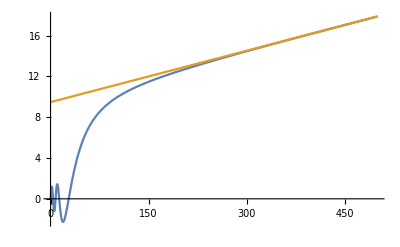

```mathematica
Plot[{p0[r],0.016792727957993418(r+564.4137015681048)},{r,0,500}]
```

This has 4 zero crossings thus there are 4 bound states

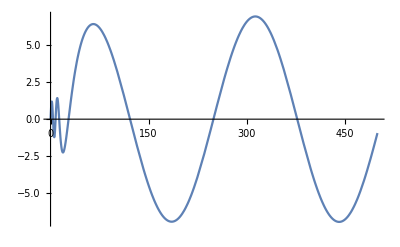
{-Graphics-,676.624}

```mathematica
e = 0.001; With [{e1=0.0003},p0[r_]=NDSolve[{-1/2 p''[r]-9.5/(27.2(1+(r/10)^4))p[r]==e1*p[r],p[0]==0,p'[0]==1},p[r],{r,0,500}][[1,1,2]];{Plot[p0[r],{r,0,500}],(4π)/(2*e1)Sin[√(2e1)FindRoot[p0[r]==0,{r,300}][[1,2]]]^2}]
```

```mathematica
Table[p0[r_]=NDSolve[{-1/2 p''[r]-9.5/(27.2(1+(r/10)^4))p[r]==e1*p[r],p[0]==0,p'[0]==1},p[r],{r,0,500}][[1,1,2]];(2π)/e1 Sin[√e1 352.326]^2,{e1,.0001,.01,.0001}];
```

```mathematica
PLOT = Table[p0[r_]=NDSolve[{-1/2 p''[r]-9.5/(27.2(1+(r/10)^4))p[r]==e1*p[r],p[0]==0,p'[0]==1},p[r],{r,0,500}][[1,1,2]];{e1,(2π)/e1 Sin[ArcTan[(√(2e1)p0[500])/p0'[500]]-√(2e1)500]^2},{e1,10^Range[-5,1,.03]}];
```

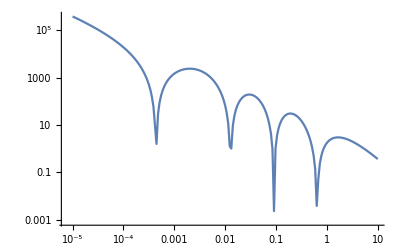

```mathematica
ListLogLogPlot[PLOT,Joined->True,PlotRange->All]
```